# chip-trap adiabatic potentials for NASA/CAL

## units and constants

```mathematica
μm=10^-6;
Gauss=10^-4;
G= Gauss;
cm = .01;
mA=mm=10^-3;
A=1;
μ0=4π 10^-7;
h = 6.62606957 10^-34;
hbar = h /(2 π);
ℏ=hbar;
kb = 1.3806488*^-23;
mRb =1.443160648*^-25;
μB=9.27400968*^-24;
gfactor=1/2;
gF = 1/2; (* not accurate to .0001 *) 
gF= gJ (F(F+1)-Inuc(Inuc+1)+J(J+1))/(2F(F+1))+gI (F(F+1)+Inuc(Inuc+1)-J(J+1))/(2F(F+1)) /. {F->2,J->1/2};
Inuc= 3/2;
Ahfs =  3.417341305*^9;
gI= -.0009951414 ;
gJ = 2.00233113;
nKPerHz = 1*^9(h/kb);






<<NathanSettings`
```

Get::noopen: Cannot open NathanSettings`.

$Failed

## three-level rotating-frame & RWA Hamiltonian (F = 1; toy)

limiting-case symmetric eigenvalues: {0,-√((Eminus1-Δ)^2+Ω^2/2),√((Eminus1-Δ)^2+Ω^2/2)}

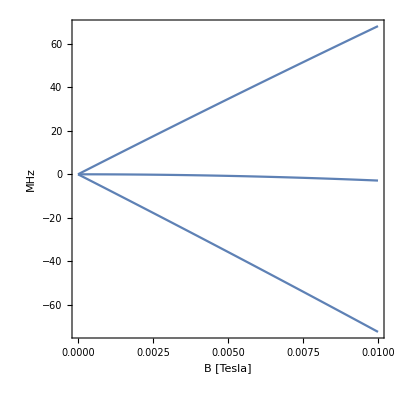

```mathematica
H0=({{Eminus1, 0, 0}, {0, E0, 0}, {0, 0, Eplus1}});
V= ({{-Δ, Ω/2, 0}, {Ω /2, 0, Ω/2}, {0, Ω/2, Δ}}); (* 1cm coil a few mm away from atoms *)
H = H0+V;

Print["limiting-case symmetric eigenvalues: ",FullSimplify[Eigenvalues[H /.{E0->0,Eplus1->-Eminus1}],{Eminus1>0,Ω>0}]]

ZeemanShift[Field_]:= {
Ahfs+ ( -gI μB Field/h-Ahfs √(1-((gJ-gI)μB/Ahfs/h/2) Field+( (gJ-gI)μB/Ahfs/h/2)^2 Field^2)),
Ahfs-Ahfs √(1+((gJ-gI)μB/Ahfs/h/2)^2 Field^2),
Ahfs+ (gI μB Field/h-Ahfs √(1+((gJ-gI)μB/Ahfs/h/2) Field+( (gJ-gI)μB/Ahfs/h/2)^2 Field^2))} (* F=1, m= -1, 0, +1 *)


Plot[ZeemanShift[Field]/1*^6,{Field,0,100 Gauss},Frame->True,FrameLabel->{"B [Tesla]","MHz"},AspectRatio->1]
```

## Zeeman-shift formulae (Breit-Rabi)

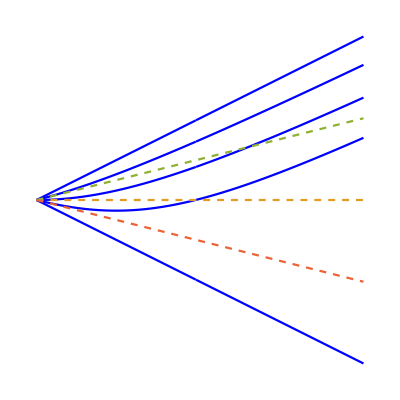

```mathematica
k = ((gJ-gI)μB/Ahfs/h/2);
Ξ[Field_]:= If[Field≥ 1/k, -1,1];
Clear[ZeemanShift];

ZeemanShift[Field_]= {
-Ahfs-2gI μB Field/h+Ξ[Field]Ahfs √(1- 2k Field+k^2 Field^2),
-Ahfs-gI μB Field/h+Ahfs √(1- k Field+k^2 Field^2),
-Ahfs+Ahfs √(1+k^2 Field^2),
-Ahfs+ gI μB Field/h+Ahfs √(1+k  Field+k^2 Field^2),
-Ahfs+ 2 gI μB Field/h+ Ahfs √(1+2k  Field+k^2 Field^2)
}; (* F=2, m= -2, -1, 0, +1, +2 *)
ZeemanShiftC = Compile[{Field},Evaluate[ZeemanShift[Field]]];  
Plot[{ZeemanShift[Field]/1*^6,0, gF(μB/h/1*^6) Field,-gF(μB/h/1*^6) Field},{Field,0,5000 Gauss},FrameLabel->{"B (Tesla)","MHz"},PlotStyle->{Blue,Dashed,Dashed,Dashed},FrameTicksStyle->Directive[Black,FontFamily->"Century Gothic"],FrameStyle->Directive[Black,15,FontFamily->"Century Gothic"],AspectRatio->1,PlotRange->All,Axes->False]
```

## magnetic field from the chip (i)

### Biot-Savart Functions

```mathematica
(* Function FatXwire calculates the B-field at position (x0,y0,z0) for a conductor of width 2*hw at position y=yc running a finite length in x from x1->x2. We assume the conductor lies in the plane z=0. *)
FatXwire[x0_,y0_,z0_,hw_,yc_,x1_,x2_]:=Module[{dx1,dx2,dyPlus,dyMinus},
dx1=-(x0-x1);
dx2=-(x0-x2);
dyPlus=-(y0-(yc+hw));
dyMinus=y0-(yc-hw);
Return[10^-3/(2hw){0,ArcTan[(dx1 dyMinus)/(z0 √(dx1^2+dyMinus^2+z0^2))]-ArcTan[(dx2 dyMinus)/(z0 √(dx2^2+dyMinus^2+z0^2))]+ArcTan[(dx1 dyPlus)/(z0 √(dx1^2+dyPlus^2+z0^2))]-ArcTan[(dx2 dyPlus)/(z0 √(dx2^2+dyPlus^2+z0^2))],Log[(dx1+√(dx1^2+dyMinus^2+z0^2))/(dx2+√(dx2^2+dyMinus^2+z0^2))(dx2+√(dx2^2+dyPlus^2+z0^2))/(dx1+√(dx1^2+dyPlus^2+z0^2))]}];
];
```

```mathematica
(* Function FatYwire calculates the magnetic field at position (x0,y0,z0) of a rectangular conductor with finite width 2*hw.  We assume: (1) Current flows in the y direction from y1 -> y2; (2) The conductor is centered at x=xc and has width 2*hw; (3) The conductor lies entirely in the x-y plane (i.e. z=0). *)
FatYwire[x0_,y0_,z0_,hw_,xc_,y1_,y2_]:=Module[{dxPlus,dxMinus,dy1,dy2},
dxPlus=hw+x0-xc;
dxMinus=hw-x0+xc;
dy1=y0-y1;
dy2=-y0+y2;
Return[10^-3/(2 hw){ArcTan[(dxPlus dy1)/(z0 √(dxPlus^2+dy1^2+z0^2))]+ArcTan[(dxMinus dy1)/(z0 √(dxMinus^2+dy1^2+z0^2))]+ArcTan[(dxPlus dy2)/(z0 √(dxPlus^2+dy2^2+z0^2))]+ArcTan[(dxMinus dy2)/(z0 √(dxMinus^2+dy2^2+z0^2))],0,-Log[(-dy1+√(dxPlus^2+dy1^2+z0^2))/(-dy1+√(dxMinus^2+dy1^2+z0^2))(dy2+√(dxMinus^2+dy2^2+z0^2))/(dy2+√(dxPlus^2+dy2^2+z0^2))]}];
];
```

### Wire Pattern

Pick a coordinate system: "x" is the direction of the main chip wire, and "y" is the direction current flows along the dimple.

#### FLIGHT CHIP T - TRAP?

```mathematica
ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
    Ix*FatXwire[x,y,z,50μm,0,-4.5mm,+3.5mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-4.5mm,-10mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,3.5mm,0mm,10mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-10mm,0mm]+{Bx,By,Bz}; (* T wire *)
+Iy*FatXwire[x,y,z,50μm,0,0mm,3.5mm]+{Bx,By,Bz}; (* T wire *)
Return[Sqrt[VecField.VecField]]
]

ChipTrapVecField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
    Ix*FatXwire[x,y,z,50μm,0,-4.5mm,+3.5mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-4.5mm,-10mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,3.5mm,0mm,10mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-10mm,0mm]+{Bx,By,Bz}; (* T wire *)
+Iy*FatXwire[x,y,z,50μm,0,0mm,3.5mm]+{Bx,By,Bz}; (* T wire *)
Return[VecField]
]
```

#### FLIGHT CHIP H - TRAP

```mathematica
XXGrad = 0.00005(* in G/cm *) ;
YYGrad=0.00005;
ZZGrad = 0.00005;
ZYGrad = 0.00005;
XGrad=XXGrad;
ZGrad=ZZGrad;
YGrad=YYGrad;

ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
   Ix*FatXwire[x,y,z,50μm,0,-13.3mm/2,+13.3mm/2] (* main section of Z wire *)
+ Ix*FatYwire[x,y,z,50μm,-13.3mm/2,-12mm,0mm] (* first leg of Z wire *)
+ Ix*FatYwire[x,y,z,50μm,13.3mm/2,0mm,12mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z+425 μm,200μm,-1.6mm,-12mm,12mm] (* first leg of H *)
+Iy*FatYwire[x,y,z+425 μm,200μm,1.6mm,-12mm,12mm] (* second leg of H *)
+{Bx,By,Bz}+{100 XGrad x , 100 YGrad y ,100 ZGrad z+100ZYGrad y};
Return[Sqrt[VecField.VecField]]
]

ChipTrapVecField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
   Ix*FatXwire[x,y,z,50μm,0,-13.3mm/2,+13.3mm/2] (* main section of Z wire *)
+ Ix*FatYwire[x,y,z,50μm,-13.3mm/2,-12mm,0mm] (* first leg of Z wire *)
+ Ix*FatYwire[x,y,z,50μm,13.3mm/2,0mm,12mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z+425 μm,200μm,-1.6mm,-12mm,12mm] (* first leg of 2nd Z wire *)
+Iy*FatYwire[x,y,z+425 μm,200μm,1.6mm,-12mm,12mm] (* second leg of 2nd Z wire *)
+{Bx,By,Bz}+{100 XXGrad x ,100 YYGrad y ,100ZZGrad z+100ZYGrad y};
Return[VecField]
]
```

```mathematica
(* Plot3D[ChipTrapField[x,y,0.0005,-3.3,-1.3,-22.6 ,-1.6 22.6,0],{x,-10mm,10mm},{y,-1mm,1mm},PlotRange->All,PlotPoints->40]  *)
```

#### SM3

```mathematica
XXGrad = 0.00005(* in G/cm *) ;
YYGrad=0.00005;
ZZGrad = 0.00005;
ZYGrad = 0.00005;
XGrad=XXGrad;
ZGrad=ZZGrad;
YGrad=YYGrad;

Hoffset = -425 μm;
WireWidth = 50 μm; (*half-width*)

ChipTrapField[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=Module[{VecField},
 VecField=
   Izb FatXwire[x,y,z,WireWidth,0,-5.5mm,+5.5mm] (* main section of Z wire *)
+ Izb FatYwire[x,y,z,WireWidth,-5.5mm,-5mm,0 mm] (* first leg of Z wire *)
+ Izb FatYwire[x,y,z,WireWidth,5.5mm,0mm,5mm] (* second leg of Z wire *)
+Ih FatYwire[x,y,z-Hoffset,200μm,-1.5mm,5mm,-5mm] (* first leg of H *)
+Ih FatYwire[x,y,z-Hoffset,200μm,1.5mm,5mm,-5mm] (* second leg of H *)
+ Ilb FatXwire[x,y,z,WireWidth,-150 μm,75 μm,+5.5mm] (* main section of L wire *)
+ Ilb FatYwire[x,y,z,WireWidth,75 μm,-5mm,-150μm] (* first leg of L wire *)
+ Ilb FatYwire[x,y,z,WireWidth,5.5mm,-150 μm,-5mm] (* second leg of L wire *)
+{Bx,By,Bz}+{100 XGrad x , 100 YGrad y ,100 ZGrad z+100ZYGrad y};
Return[Sqrt[VecField.VecField]]
]

ChipTrapVecField[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=Module[{VecField},
 VecField=
   Izb FatXwire[x,y,z,WireWidth,0,-5.5mm,+5.5mm] (* main section of Z wire *)
+ Izb FatYwire[x,y,z,WireWidth,-5.5mm,-5mm,0 mm] (* first leg of Z wire *)
+ Izb FatYwire[x,y,z,WireWidth,5.5mm,0mm,5mm] (* second leg of Z wire *)
+Ih FatYwire[x,y,z-Hoffset,200μm,-1.5mm,5mm,-5mm] (* first leg of H *)
+Ih FatYwire[x,y,z-Hoffset,200μm,1.5mm,5mm,-5mm] (* second leg of H *)
+ Ilb FatXwire[x,y,z,WireWidth,-150 μm,75 μm,+5.5mm] (* main section of L wire *)
+ Ilb FatYwire[x,y,z,WireWidth,75 μm,-5mm,-150μm] (* first leg of L wire *)
+ Ilb FatYwire[x,y,z,WireWidth,5.5mm,-150 μm,-5mm] (* second leg of L wire *)
+{Bx,By,Bz}+{100 XGrad x , 100 YGrad y ,100 ZGrad z+100ZYGrad y};
Return[VecField]
]
```

### Full chip (Murphree)

```mathematica
ChipTrapFieldAAndB[x_,y_,z_,Ila_,Iza_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=Module[
{VecField,
ZLength,LLength,LegLength,deltaL,
ZAMainyc,ZAMainx0,ZAMainx1,
ZALeg1xc,ZALeg1y0,ZALeg1y1,
ZALeg2xc,ZALeg2y0,ZALeg2y1,
LAMainyc,LAMainx0,LAMainx1,
LALeg1xc,LALeg1y0,LALeg1y1,
LALeg2xc,LALeg2y0,LALeg2y1,
ZBMainyc,ZBMainx0,ZBMainx1,
ZBLeg1xc,ZBLeg1y0,ZBLeg1y1,
ZBLeg2xc,ZBLeg2y0,ZBLeg2y1,
LBMainyc,LBMainx0,LBMainx1,
LBLeg1xc,LBLeg1y0,LBLeg1y1,
LBLeg2xc,LBLeg2y0,LBLeg2y1},
ZLength=11.55mm;
LLength=5.875mm;
LegLength=5mm;
deltaL=150μm;(* Distance between the centers of two adjacent wires *)

{LALeg1xc,LALeg1y0,LALeg1y1}={-deltaL/2,2000μm+deltaL+LegLength,2000μm+deltaL}; (* Took separation of lines before the bend, which is indicated in the diagram, to be the same after the bend. *)
{LAMainyc,LAMainx0,LAMainx1}={LALeg1y1,LALeg1xc,LALeg1xc-LLength};
{LALeg2xc,LALeg2y0,LALeg2y1}={LAMainx1,LAMainyc,LALeg1y0};

{ZAMainyc,ZAMainx0,ZAMainx1}={2000μm,-deltaL/2-LLength+ZLength,-deltaL/2-LLength};
{ZALeg1xc,ZALeg1y0,ZALeg1y1}={ZAMainx0,ZAMainyc+LegLength,ZAMainyc};
{ZALeg2xc,ZALeg2y0,ZALeg2y1}={ZAMainx1,ZAMainyc,ZAMainyc-LegLength};

{LBLeg1xc,LBLeg1y0,LBLeg1y1}={deltaL/2,-deltaL-LegLength,-deltaL};
{LBMainyc,LBMainx0,LBMainx1}={LBLeg1y1,LBLeg1xc,LBLeg1xc+LLength};
{LBLeg2xc,LBLeg2y0,LBLeg2y1}={LBMainx1,LBMainyc,LBLeg1y0};

{ZBMainyc,ZBMainx0,ZBMainx1}={0,deltaL/2+LLength-ZLength,deltaL/2+LLength};
{ZBLeg1xc,ZBLeg1y0,ZBLeg1y1}={ZBMainx0,ZBMainyc-LegLength,ZBMainyc};
{ZBLeg2xc,ZBLeg2y0,ZBLeg2y1}={ZBMainx1,ZBMainyc,ZBMainyc+LegLength};



 VecField=(
Iza FatXwire[x,y,z,WireWidth,ZAMainyc,ZAMainx0,ZAMainx1](* main section of ZA wire *)
+ Iza FatYwire[x,y,z,WireWidth,ZALeg1xc,ZALeg1y0,ZALeg1y1](* first leg of ZA wire *)
+Iza FatYwire[x,y,z,WireWidth,ZALeg2xc,ZALeg2y0,ZALeg2y1](* second leg of ZA wire *)

+Ila FatXwire[x,y,z,WireWidth,LAMainyc,LAMainx0,LAMainx1](* main section of LA wire *)
+Ila FatYwire[x,y,z,WireWidth,LALeg1xc,LALeg1y0,LALeg1y1](* first leg of LA wire *)
+Ila FatYwire[x,y,z,WireWidth,LALeg2xc,LALeg2y0,LALeg2y1](* second leg of LA wire *)

+Izb FatXwire[x,y,z,WireWidth,ZBMainyc,ZBMainx0,ZBMainx1](* main section of ZB wire *)
+ Izb FatYwire[x,y,z,WireWidth,ZBLeg1xc,ZBLeg1y0,ZBLeg1y1](* first leg of ZB wire *)
+Izb FatYwire[x,y,z,WireWidth,ZBLeg2xc,ZBLeg2y0,ZBLeg2y1](* second leg of ZB wire *)

+Ilb FatXwire[x,y,z,WireWidth,LBMainyc,LBMainx0,LBMainx1](* main section of LB wire *)
+Ilb FatYwire[x,y,z,WireWidth,LBLeg1xc,LBLeg1y0,LBLeg1y1](* first leg of LB wire *)
+Ilb FatYwire[x,y,z,WireWidth,LBLeg2xc,LBLeg2y0,LBLeg2y1](* second leg of LB wire *)

+Ih FatYwire[x,y,z-Hoffset,200μm,-1.5mm,5mm,-5mm] (* first leg of H *)
+Ih FatYwire[x,y,z-Hoffset,200μm,1.5mm,5mm,-5mm] (* second leg of H *)

+{Bx,By,Bz}+{100 XGrad x , 100 YGrad y ,100 ZGrad z+100ZYGrad y});(* Bias fields and field gradients *)
Return[Sqrt[VecField.VecField]]
]
```

```mathematica
ChipTrapVecFieldAAndB[x_,y_,z_,Ila_,Iza_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=Module[
{VecField,
ZLength,LLength,LegLength,deltaL,
ZAMainyc,ZAMainx0,ZAMainx1,
ZALeg1xc,ZALeg1y0,ZALeg1y1,
ZALeg2xc,ZALeg2y0,ZALeg2y1,
LAMainyc,LAMainx0,LAMainx1,
LALeg1xc,LALeg1y0,LALeg1y1,
LALeg2xc,LALeg2y0,LALeg2y1,
ZBMainyc,ZBMainx0,ZBMainx1,
ZBLeg1xc,ZBLeg1y0,ZBLeg1y1,
ZBLeg2xc,ZBLeg2y0,ZBLeg2y1,
LBMainyc,LBMainx0,LBMainx1,
LBLeg1xc,LBLeg1y0,LBLeg1y1,
LBLeg2xc,LBLeg2y0,LBLeg2y1},
ZLength=11.55mm;
LLength=5.875mm;
LegLength=5mm;
deltaL=150μm;(* Distance between the centers of two adjacent wires *)

{LALeg1xc,LALeg1y0,LALeg1y1}={-deltaL/2,2000μm+deltaL+LegLength,2000μm+deltaL}; (* Took separation of lines before the bend, which is indicated in the diagram, to be the same after the bend. *)
{LAMainyc,LAMainx0,LAMainx1}={LALeg1y1,LALeg1xc,LALeg1xc-LLength};
{LALeg2xc,LALeg2y0,LALeg2y1}={LAMainx1,LAMainyc,LALeg1y0};

{ZAMainyc,ZAMainx0,ZAMainx1}={2000μm,-deltaL/2-LLength+ZLength,-deltaL/2-LLength};
{ZALeg1xc,ZALeg1y0,ZALeg1y1}={ZAMainx0,ZAMainyc+LegLength,ZAMainyc};
{ZALeg2xc,ZALeg2y0,ZALeg2y1}={ZAMainx1,ZAMainyc,ZAMainyc-LegLength};

{LBLeg1xc,LBLeg1y0,LBLeg1y1}={deltaL/2,-deltaL-LegLength,-deltaL};
{LBMainyc,LBMainx0,LBMainx1}={LBLeg1y1,LBLeg1xc,LBLeg1xc+LLength};
{LBLeg2xc,LBLeg2y0,LBLeg2y1}={LBMainx1,LBMainyc,LBLeg1y0};

{ZBMainyc,ZBMainx0,ZBMainx1}={0,deltaL/2+LLength-ZLength,deltaL/2+LLength};
{ZBLeg1xc,ZBLeg1y0,ZBLeg1y1}={ZBMainx0,ZBMainyc-LegLength,ZBMainyc};
{ZBLeg2xc,ZBLeg2y0,ZBLeg2y1}={ZBMainx1,ZBMainyc,ZBMainyc+LegLength};



 VecField=(
Iza FatXwire[x,y,z,WireWidth,ZAMainyc,ZAMainx0,ZAMainx1](* main section of ZA wire *)
+ Iza FatYwire[x,y,z,WireWidth,ZALeg1xc,ZALeg1y0,ZALeg1y1](* first leg of ZA wire *)
+Iza FatYwire[x,y,z,WireWidth,ZALeg2xc,ZALeg2y0,ZALeg2y1](* second leg of ZA wire *)

+Ila FatXwire[x,y,z,WireWidth,LAMainyc,LAMainx0,LAMainx1](* main section of LA wire *)
+Ila FatYwire[x,y,z,WireWidth,LALeg1xc,LALeg1y0,LALeg1y1](* first leg of LA wire *)
+Ila FatYwire[x,y,z,WireWidth,LALeg2xc,LALeg2y0,LALeg2y1](* second leg of LA wire *)

+Izb FatXwire[x,y,z,WireWidth,ZBMainyc,ZBMainx0,ZBMainx1](* main section of ZB wire *)
+ Izb FatYwire[x,y,z,WireWidth,ZBLeg1xc,ZBLeg1y0,ZBLeg1y1](* first leg of ZB wire *)
+Izb FatYwire[x,y,z,WireWidth,ZBLeg2xc,ZBLeg2y0,ZBLeg2y1](* second leg of ZB wire *)

+Ilb FatXwire[x,y,z,WireWidth,LBMainyc,LBMainx0,LBMainx1](* main section of LB wire *)
+Ilb FatYwire[x,y,z,WireWidth,LBLeg1xc,LBLeg1y0,LBLeg1y1](* first leg of LB wire *)
+Ilb FatYwire[x,y,z,WireWidth,LBLeg2xc,LBLeg2y0,LBLeg2y1](* second leg of LB wire *)

+Ih FatYwire[x,y,z-Hoffset,200μm,-1.5mm,5mm,-5mm] (* first leg of H *)
+Ih FatYwire[x,y,z-Hoffset,200μm,1.5mm,5mm,-5mm] (* second leg of H *)

+{Bx,By,Bz}+{100 XGrad x , 100 YGrad y ,100 ZGrad z+100ZYGrad y});(* Bias fields and field gradients *)
Return[VecField]
]
```

#### CAREFUL: UNDEFINE TO MATCH NATHAN’S

```mathematica
ChipTrapField[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=ChipTrapFieldAAndB[x,y,z,0,0,Ilb,Izb,Ih,Bx,By,Bz];
ChipTrapVecField[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=ChipTrapVecFieldAAndB[x,y,z,0,0,Ilb,Izb,Ih,Bx,By,Bz];
```

#### Plot full chip fields

```mathematica
plotBound=6.5;
Plot3D[ChipTrapFieldAAndB[x mm,y mm,.005 mm,CurrL,CurrZ,CurrL,CurrZ,CurrH,Bx1,By1,Bz1 ],{x,-plotBound,plotBound},{y,-plotBound,plotBound},PlotRange->All,PlotPoints->30,AxesLabel->{"X","Y","B"}, BoundaryStyle->Directive[Green,Thick],AspectRatio->1]

plotBound=0.5;
Plot3D[ChipTrapFieldAAndB[x mm,y mm,.005 mm,CurrL,CurrZ,CurrL,CurrZ,CurrH,Bx1,By1,Bz1 ],{x,-plotBound,plotBound},{y,-plotBound,plotBound},PlotRange->All,PlotPoints->30,AxesLabel->{"X","Y","B"}, BoundaryStyle->Directive[Green,Thick],AspectRatio->1]

Plot3D[ChipTrapFieldAAndB[x mm,y mm,.005 mm,CurrL,CurrZ,CurrL,CurrZ,CurrH,Bx1,By1,Bz1 ],{x,-plotBound,plotBound},{y,-plotBound+2,plotBound+2},PlotRange->All,PlotPoints->30,AxesLabel->{"X","Y","B"}, BoundaryStyle->Directive[Green,Thick],AspectRatio->1]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

### Plot chip fields

```mathematica
(* Helps position cloud (the ellipsoid, though it will appear as an x-y cross-section at 0.005mm) within the trapping potential.?*)
Show[{Plot3D[ChipTrapField[x mm,y mm,.005 mm,CurrL,CurrZ, CurrH,Bx1,By1,Bz1 ],{x,-.5,.5},{y,-.5,.5},PlotRange->All,PlotPoints->30,AxesLabel->{"X","Y","B"}, BoundaryStyle->Directive[Green,Thick],AspectRatio->1]  ,Graphics3D[Ellipsoid[{x1/mm,y1/mm,ChipTrapField[x1,y1,z1,CurrL,CurrZ,CurrH,Bx1,By1,Bz1]},{.2,.2,1}]]}]
```

-Graphics3D-

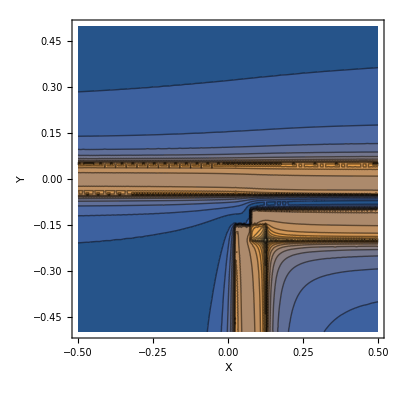

```mathematica
ContourPlot[Abs[ChipTrapField[x mm,y mm,.001 mm,1,1, 0,0,0,0 ]],{x,-.5,.5},{y,-.5,.5},PlotRange->All,PlotPoints->15,Contours->20,AxesLabel->{"X","Y"}]
```

#### GTB CHIP x - TRAP (this is now the flight chip)?

```mathematica
ChipTrapField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
    Ix*FatXwire[x,y,z,50μm,0,-1.075mm,+1.075mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-1.075 mm,-6mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,1.075mm,0mm,6mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-6mm,6mm]+{Bx,By,Bz}; (* dimple wire *)
Return[Sqrt[VecField.VecField]]
]

ChipTrapVecField[x_,y_,z_,Ix_,Iy_,Bx_,By_,Bz_]:=Module[{VecField},
VecField=
    Ix*FatXwire[x,y,z,50μm,0,-1.075mm,+1.075mm] (* main section of Z wire *)
+Ix*FatYwire[x,y,z,50μm,-1.075 mm,-6mm,0mm] (* first leg of Z wire *)
+Ix*FatYwire[x,y,z,50μm,1.075mm,0mm,6mm] (* second leg of Z wire *)
+Iy*FatYwire[x,y,z,50μm,0,-6mm,6mm]+{Bx,By,Bz}; (* dimple wire *)
Return[VecField]
]
```

```mathematica
(* {CLg1,CLd1,Bx1,By1,Bz1}   *)
```

```mathematica
(* Plot3D[ChipTrapField[x,y,0.0005,3.2,-0.362,10.74 ,36,0.],{x,-10mm,10mm},{y,-2mm,2mm},PlotRange->All,PlotPoints->60,AxesLabel->{"x","y","z"}]   *)
```

### Trap Position

```mathematica
z0[Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=NMinimize[{ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],-.4 mm<x<.4mm,-.4mm<y<1.5mm,2500μm>z>20μm},{x,y,z}][[2]](* Returns the spatial coordinates {xmin, ymin, zmin} of the chip's magnetic field minimum. *)
```

### Trap Frequencies & Field/Vector Functions

```mathematica
Dxx[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],{x,2}];
Dxy[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],x,y];
Dxz[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],x,z];
Dyy[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],{y,2}];
Dyz[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],y,z];
Dzz[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=D[10^-4 ChipTrapField[x,y,z,Ilb,Izb,Ih,Bx,By,Bz],{z,2}];
DMatrix[x_,y_,z_,Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:=({{Dxx[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dxy[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dxz[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]}, {Dxy[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dyy[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dyz[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]}, {Dxz[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dyz[x,y,z,Ilb,Izb,Ih,Bx,By,Bz], Dzz[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]}});

(* The function ChipTrapFrequencies calculates the position z0 where the trap is centered. It does this using the values for the chip currents and bias fields. It assumes the trap is centered at x=0 and y=0 *)




ChipTrapFrequencies[Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:= Module[
{x,y,z,DMatrixDiag,xmin,ymin,zmin,DMatrix0,e1,e2,e3},
{xmin,ymin,zmin}=z0[Ilb,Izb,Ih,Bx,By,Bz];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrix0=SchurDecomposition[DMatrix[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]/.{x->xmin,y->ymin,z->zmin}];
DMatrixDiag=DMatrix0[[2]];
e1=DMatrix0[[1,1]];
e2=DMatrix0[[1,2]];
e3=DMatrix0[[1,3]];
Return[
 {{ϕ,(180/Pi)ArcTan[e1[[2]]/e1[[1]]]//Round,
θ,(180/Pi)ArcCos[e1[[3]]/Sqrt[e1[[1]]^2+e1[[2]]^2+e1[[3]]^2]]//Round},

{ϕ,(180/Pi)ArcTan[e2[[2]]/e2[[1]]]//Round,
θ,(180/Pi)ArcCos[e2[[3]]/Sqrt[e2[[1]]^2+e2[[2]]^2+e2[[3]]^2]]//Round},

{ϕ,(180/Pi)ArcTan[e3[[2]]/e3[[1]]]//Round,
θ,(180/Pi)ArcCos[e3[[3]]/Sqrt[e3[[1]]^2+e3[[2]]^2+e3[[3]]^2]]//Round},


Diagonal[Sqrt[μB Abs[DMatrixDiag]/mRb]/(2π) ]}(* in Hz *)
]
]

ChipTrapFrequenciesRawPrincipleAxes[Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:= Module[
{x,y,z,DMatrixDiag,xmin,ymin,zmin,DMatrix0,e1,e2,e3,eVals},
{xmin,ymin,zmin}=z0[Ilb,Izb,Ih,Bx,By,Bz];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrix0=SchurDecomposition[DMatrix[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]/.{x->xmin,y->ymin,z->zmin}];
DMatrixDiag=DMatrix0[[2]];
e1=DMatrix0[[1,1]];
e2=DMatrix0[[1,2]];
e3=DMatrix0[[1,3]];
eVals=Diagonal[Sqrt[μB Abs[DMatrixDiag]/mRb]/(2π) ];(* in Hz *)
Return[
 {{e1,eVals⟦1⟧},{e2,eVals⟦2⟧},{e3,eVals⟦3⟧}}
]
]

ChipTrapFrequenciesOld[Ilb_,Izb_,Ih_,Bx_,By_,Bz_]:= Module[
{x,y,z,DMatrixDiag,xmin,ymin,zmin},
{xmin,ymin,zmin}=z0[Ilb,Izb,Ih,Bx,By,Bz];
xmin=xmin[[2]];
ymin=ymin[[2]];
zmin=zmin[[2]];
DMatrixDiag=Eigensystem[DMatrix[x,y,z,Ilb,Izb,Ih,Bx,By,Bz]/.{x->xmin,y->ymin,z->zmin}];
Return[
 Sqrt[μB Abs[DMatrixDiag[[1]]]/mRb]/(2π) (* in Hz *)
]
]


BChipMag[x_, y_, z_] :=ChipTrapField[x, y, z, CurrL, CurrZ,CurrH, Bx1, By1, Bz1] Gauss;  
BChipMagC=Compile[{x,y,z},Evaluate[BChipMag[x,y,z]]]; 
BChipMagC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=BChipMagC[x,y,z];
 
BChip[x_, y_, z_] :=   ChipTrapVecField[x, y, z, CurrL, CurrZ, CurrH,Bx1, By1, Bz1] Gauss;
BChipDirection[x_, y_, z_] := BChip[x, y, z]/BChipMag[x, y, z]
XCosine[x_,y_,z_]:=Sin[ArcCos[Dot[BChipDirection[x,y,z],{0,0,1}]]];    (* not necessarily relevant unless approximating *)

(*Bmin1=ChipTrapField[x1,y1,z1,CurrL,CurrZ,CurrH,Bx1,By1,Bz1 ]*)
(*B0 = BChipMag[x1,y1,z1];*)
```

## magnetic field from the rf loop (for z-dependence and directional concerns)

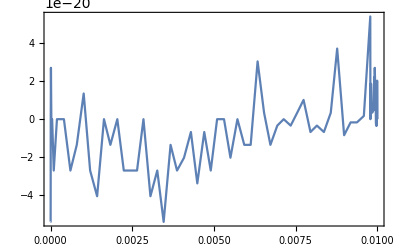

-Graphics-

```mathematica
i =1;
β[z_,z0_,a_]:=(z-z0)/a;
α[r_,a_]:=r/a;
γ[z_,z0_,r_]:=(z-z0)/r;
B[a_]:=i*μ0/(2a);
Q[z_,z0_,r_,a_]:=(1+α[r,a])^2+β[z,z0,a]^2;
d[z_,z0_,r_,a_]:=(4α[r,a])/Q[z,z0,r,a];

Bz[z_,z0_,r_,a_]:=B[a]*(1/(π*√Q[z,z0,r,a]))*((EllipticE[d[z,z0,r,a]])((1-α[r,a]^2-β[z,z0,a]^2)/(Q[z,z0,r,a]-4α[r,a]))+EllipticK[d[z,z0,r,a]])

Br[z_,z0_,r_,a_]:=B[a]*(γ[z,z0,r]/(π*√Q[z,z0,r,a]))*((EllipticE[d[z,z0,r,a]])*((1+α[r,a]^2+β[z,z0,a]^2)/(Q[z,z0,r,a]-4α[r,a]))-EllipticK[d[z,z0,r,a]]) (* When on-axis, Br=0*)
Bmag[z_,z0_,r_,a_]:=√((Bz[z,z0,r,a])^2+(Br[z,z0,r,a])^2) (*magnitude of total magnetic field*)

Btest[z_,z0_,a_]:=(μ0 i/2) a^2/(a^2 + (z-z0)^2)^1.5;
Plot[Bmag[z,0,1*^-10,.005]-Btest[z,0,.005],{z,0,.01},Frame->True]
Plot[(h /kb/1*^-9)(15000Bmag[z,LoopOriginZ,1*^-10,.005]/Bmag[z1,LoopOriginZ,1*^-10,.005] - 15000),{z,0.000660,.000860},Frame->True,Axes->False,PlotStyle->Thickness[.02]]
```

```mathematica
Plot[(Bmag[z,LoopOriginZ,x1+.00001,.005]/Bmag[z1,LoopOriginZ,x1+.00001,.005] ),{z,-.010,.010},Frame->True,Axes->False,PlotStyle->Thickness[.01](*,GridLines->{{0,z1},{1.0,z1}}*)]
```

-Graphics-

```mathematica
LoopRadius = 1.5 5.0 mm; (* 5.0 default from SM2 *)
LoopOriginZ = -3.0 mm;
```

```mathematica
RFUnitVec[x_,y_,z_]:={
Br[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius] x/Sqrt[x^2+y^2],
Br[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius] y/Sqrt[x^2+y^2] , 
Bz[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]
}/Bmag[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]

XCosineAccurate[x_,y_,z_]:=Sin[ArcCos[Dot[BChipDirection[x,y,z],RFUnitVec[x,y,z]]]];  (* projection between local field and ideally-orthogonal rf polarization *)
GermanAngle[x_,y_,z_]:=ArcCos[Dot[BChipDirection[x,y,z],RFUnitVec[x,y,z]]];  (* projection between local field and ideally-orthogonal rf polarization *)
XCosineAccurateC=Compile[{x,y,z},Evaluate[XCosineAccurate[x,y,z]]];
XCosineAccurateC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:= XCosineAccurateC[x,y,z];
```

## magnetic field from the chip (ii)

```mathematica
(* wacky *)
Ldec=0.5;
Zdec=1.1;
Hdec =1.0;

CurrL= Ldec    0.85A ;(* L wire current  0.85 default *) 
CurrZ=Zdec     2.4A;  (* z wire current 2.40 default *)
CurrH=Hdec     2.3A;(* H wire current  2.3 default *)

fdec = 0.3;
Bx1=  fdec(-.22A)  40.625   ;
By1=  .4fdec (2.567A)  14.286 ;
Bz1=  fdec (.2 A ) 10.3675;




(* modified ZH *)
CurrL = 0.5 A ;(* L wire current  0.85 default *) 
CurrZ =     2.3 A;  (* z wire current 2.40 default *)
CurrH =     2.7 A;(* H wire current  2.3 default *)

Bx1 = 3.2 (-.048 A)  40.625   ;
By1 = .6 (0.63 A)  14.286 ;
Bz1 = (-.1 A ) 10.3675;


(* Maren Mossman's 31 G trap *)
CurrL =     0. A ;(* L wire current  0.85 default *) 
CurrZ =   3.2 A;  (* z wire current 2.40 default *)
CurrH =    1.0 A;(* H wire current  2.3 default *)
Bx1 =  (-.729 A)  40.625   ;
By1 =  (.765 A)  14.286 ;
Bz1 =   (0. A ) 10.3675;


(* ZH-b *)
CurrL = 0. A ;(* L wire current  0.85 default *) 
CurrZ =     2.6 A;  (* z wire current 2.40 default *)
CurrH =     2.3 A;(* H wire current  2.3 default *)

Bx1 = (-.048 A)  40.625   ;
By1 = (0.63 A)  14.286 ;
Bz1 = (.0003 A ) (-10.3675);




(* ZH-b Cass *)  (* pretty nice, centered in window *)

CurrL = 0.0 A ;(* L wire current  0.85 default *) 
CurrZ =     3.2A;  (* z wire current 2.40 default *)
CurrH =    1.3A;(* H wire current  2.3 default *)

Bx1 =(-.051 A)  40.625   ;
By1 =(0.195 A)  14.286 ;
Bz1 =1.0(.375 A ) (-10.3675);   (* sign disagreement here? *) 

(* ZH-b run by Rob on April 10 *)
(* Centered at the origin and has aspect ratio 4.4 "not great" *)
CurrL = 0. A; (* L wire current   0.85 default *)
CurrZ = 2.6 A; (* z wire urrent 2.40 default *)
CurrH = 2.3 A; (* H wire current   2.3 default *)

Bx1 = (-0.048 A) 40.625;
By1 = (0.63 A) 14.286;
Bz1 = (-0.0003 A) (-10.3675);

(* ZH Nathan *)
(* Pushed out a little in y, but not all the way to the center *)
(* Not clear how far out in y one needs to go to be visible to the hi-res cam *)
CurrL = 0.0 A; (* L wire current  0.85 default *)
CurrZ = 2.6 A; (* z wire current 2.40 default *)
CurrH = 2.6 A; (* H wire current  2.3 default *)

Bx1 = (-0.048 A) 40.625;
By1 = (0.43 A) 14.286;
Bz1 = (0.3003 A) (-10.3675);

(* ZZH ZZH DO THIS DO THIS DO THIS?? *) 



(*(* default  "Decompressed ZLH-b" *)
Ldec = 1.0;
Zdec = 1.0;
Hdec = 1.0;

CurrL = Ldec    0.85 A ;(* L wire current  0.85 default *) 
CurrZ = Zdec     2.40 A;  (* z wire current 2.40 default *)
CurrH = Hdec     2.300 A;(* H wire current  2.3 default *)

fdec =0.2;
Bx1 = fdec (-.220 A) ( 40.625) 1.04 ;
By1 = fdec (2.567 A)  (14.286) .96 ;
Bz1 =(-.150 A ) (-10.3675) 1.09;   (* claim that a negative current here means field in +z direction *)
*)
(*(* "Decompressed ZLH-b" realized the week of 13 July 2020 *)
Ldec = 0.243;
Zdec = -.686;
Hdec = 0.460;

CurrL = Ldec*3.5 A ;(* L wire current  0.85 default *) 
CurrZ = Zdec*-3.5 A ; (* z wire current 2.40 default *)
CurrH = Hdec*5 A;(* H wire current  2.3 default *)
(* Bias coils *)
IbxMax=8.;(*[A]*)
IbyMax=3.02;(*[A]*)
IbzMax=3.;(*[A]*)

fdec =0.2;

T1=fdec*0.028
Y=fdec*0.85
Z=0

Ix=-T1*IbxMax
Iy=IbyMax*Y
Iz=IbzMax*Z

Bx1 = Ix*( 40.625);
By1 = Iy*(14.286);
Bz1 =Iz*(-10.3675);*)(*(-.150 A ) (-10.3675) 1.09;   *)(* claim that a negative current here means field in +z direction *)
```

```mathematica
<<"SMThreeChipModel.m"
```

Get::noopen: Cannot open SMThreeChipModel.m.

$Failed

```mathematica
z0AB[0,0,CurrL,CurrZ,CurrH,Bx1,By1,Bz1]⟦All,2⟧*10*^6 (* Why the unit disagreement? *)
ChipTrapABFrequencies[0,0,CurrL,CurrZ,CurrH,Bx1,By1,Bz1]
```

Part::partd: Part specification z0AB[0,0,0.,2.6,2.6,-1.95,6.14298,-3.11336]⟦All,2⟧ is longer than depth of object.

10000000 z0AB[0,0,0.,2.6,2.6,-1.95,6.14298,-3.11336]⟦All,2⟧

ChipTrapABFrequencies[0,0,0.,2.6,2.6,-1.95,6.14298,-3.11336]

```mathematica
BChipMagC=Compile[{x,y,z},Evaluate[BChipMag[x,y,z]]];
BChipMagC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=BChipMagC[x,y,z];
{x1,y1,z1}=z0[CurrL,CurrZ,CurrH,Bx1,By1,Bz1] //Chop
Print["x1 = ", Round[1000000 (x /. x1),.1], " μm"]
Print["y1 = ", Round[1000000 (y /. y1),.1], " μm"]
Print["z1 = ", Round[1000000 (z /. z1),.1], " μm"]
x1=x1[[2]];
y1=y1[[2]];
z1=z1[[2]];
Bmin1=ChipTrapField[x1,y1,z1,CurrL,CurrZ,CurrH,Bx1,By1,Bz1 ];(* Magnitude of the field at the minimum in Gauss *)
B0 = BChipMag[x1,y1,z1]; (* As far as I can tell, the same as Bmin1*Gauss, so B0 is in Tesla *)


RFUnitVec[x_,y_,z_]:={
Br[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius] x/Sqrt[x^2+y^2],
Br[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius] y/Sqrt[x^2+y^2] , 
Bz[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]
}/Bmag[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]

XCosineAccurate[x_,y_,z_]:=Sin[ArcCos[Dot[BChipDirection[x,y,z],RFUnitVec[x,y,z]]]];  (* projection between local field and ideally-orthogonal rf polarization *)
GermanAngle[x_,y_,z_]:=ArcCos[Dot[BChipDirection[x,y,z],RFUnitVec[x,y,z]]];  (* projection between local field and ideally-orthogonal rf polarization *)
XCosineAccurateC=Compile[{x,y,z},Evaluate[XCosineAccurate[x,y,z]]];
XCosineAccurateC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:= XCosineAccurateC[x,y,z];


(* MagFrac[x_,y_,z_]:=Cos[ArcSin[Br[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]/Bz[z,LoopOriginZ,Sqrt[x^2+y^2],LoopRadius]] ]Bmag[z,LoopOriginZ,Sqrt[x^2+y^2], LoopRadius]/Bmag[z1,LoopOriginZ,1*^-10, LoopRadius]; *)

MagFrac[x_,y_,z_]:=Bmag[z,LoopOriginZ,Sqrt[x^2+y^2], LoopRadius]/Bmag[z1,LoopOriginZ,1*^-10, LoopRadius]; (* Magnitude of the rf loop magnetic field at radius Sqrt[x^2+y^2] and height z, scaled by the magnitude of the same field evaluated at the trap minimum z coordinate and radius 1*^-10 (0.1 nm, effectively zero) *)
MagFracC=Compile[{x,y,z},Evaluate[MagFrac[x,y,z]]];
MagFracC2[x_?NumericQ,y_?NumericQ,z_?NumericQ]:=MagFracC[x,y,z];
MagFracSimple[x_,y_,z_]:=Bmag[z,LoopOriginZ,Sqrt[x^2+y^2], LoopRadius]/Bmag[z1,LoopOriginZ,1*^-10, LoopRadius]
```

{x→0.0000196048,y→0.000341948,z→0.000627837}

x1 = 19.6 μm

y1 = 341.9 μm

z1 = 627.8 μm

Bmin = 4.98 G

trap bottom = 3.485 MHz

Depth = 2.17 G

frequencies: {{ϕ,8,θ,87},{ϕ,-84,θ,54},{ϕ,-78,θ,36},{22.63,54.42,57.46}} Hz

Aspect Ratio = 2.54

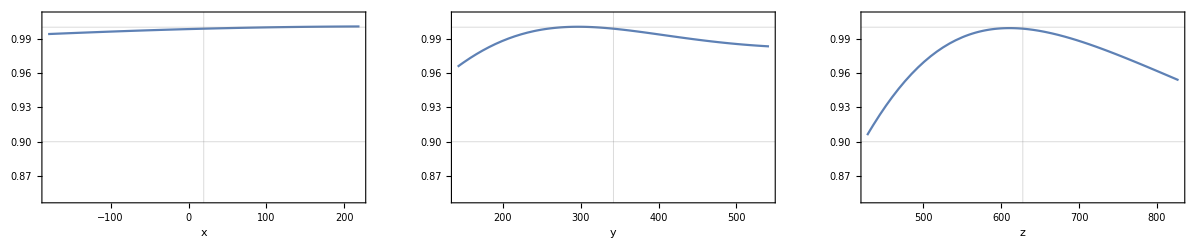

-0.341001

0.705883

0.193313

```mathematica
Print["Bmin = ", NumberForm[Bmin1,3], " G"]
Print["trap bottom = "  ,Δguess = ((ZeemanShift[B0]//Differences //Mean)/1*^3 //Round)/1000.," MHz"]
Depth1=ChipTrapField[x1,y1,1.0,CurrL,CurrZ,CurrH, Bx1,By1,Bz1 ]-Bmin1; (*The comparison field is evaluated at z=1.0 is 1 m, essentially infinity.*)
Print["Depth = ", NumberForm[Depth1,3], " G"]
freqs1=ChipTrapFrequencies[CurrL,CurrZ,CurrH, Bx1,By1,Bz1 ];
Print["frequencies: ", NumberForm[freqs1,4], " Hz"]
Print["Aspect Ratio = ", NumberForm[Max[freqs1[[4]]]/Min[freqs1[[4]]],3]]
GraphicsGrid[{{
Plot[XCosineAccurateC2[x μm,y1,z1]MagFracC2[x μm,y1,z1],{x,x1/μm-200,x1/μm+200},Axes->False,Frame->True,GridLines->{{x1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"x"}],


Plot[XCosineAccurateC2[x1,y μm,z1]MagFracC2[x1,y μm,z1]
,{y,y1/μm-200,y1/μm+200},Axes->False,Frame->True,GridLines->{{y1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"y"}],
Plot[XCosineAccurateC2[x1,y1,z μm]MagFracC2[x1,y1,z μm],{z,z1/μm-200,z1/μm+200},AxesOrigin->{z1/μm,0},Axes->False,Frame->True,GridLines->{{z1/μm},{.9,1.0}},PlotRange->{.85,1.01},FrameLabel->{"z"}]}}]
100(XCosineAccurateC2[x1-100μm,y1,z1]MagFracC2[x1-100μm,y1,z1]-XCosineAccurateC2[x1+100 μm,y1,z1]MagFracC2[x1+100 μm,y1,z1])
100(XCosineAccurateC2[x1,y1-100 μm,z1]MagFracC2[x1,y1-100 μm,z1]-XCosineAccurateC2[x1,y1+100 μm,z1]MagFracC2[x1,y1+100 μm,z1])
100(XCosineAccurateC2[x1,y1,z1-100μm]MagFracC2[x1,y1,z1-100μm]-XCosineAccurateC2[x1,y1,z1+100μm]MagFracC2[x1,y1,z1+100μm])
```

```mathematica
a=GraphicsGrid[{{
Plot1=Plot[ChipTrapField[x1,y1,z mm, CurrL, CurrZ,CurrH,Bx1,By1,Bz1],{z,0.010,1.5},
Frame->True,Axes->False,
PlotRange->{Bmin1-.5,Bmin1+0.5},
FrameLabel->{"Vertical Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Background->None],
FrameTicksStyle->Directive[FontSize->10,Background->None],
Background->White,GridLines->{{z1/mm},{}},
ImageSize->200
],
Plot2=Plot[{
ChipTrapField[x mm,y1,z1,CurrL, CurrZ,CurrH,Bx1,By1,Bz1],ChipTrapField[x1,x mm,z1,CurrL, CurrZ,CurrH,Bx1,By1,Bz1 ]},{x,-4.05,4.05},
PlotStyle->{Orange,Green},
Frame->True,Axes->False,
PlotRange->{Bmin1-.2,Bmin1+4.0},
FrameLabel->{"Transverse Distance (mm)","Magnetic Field (G)"},
LabelStyle->Directive[FontFamily->"Arial",FontSize->10,Background->None],
FrameTicksStyle->Directive[FontSize->10,Background->None],GridLines->{{x1/mm,y1/mm},{}},
Background->White,
ImageSize->200
],
ContourPlot[ChipTrapField[x mm,y mm,z1,CurrL, CurrZ,CurrH,Bx1,By1,Bz1],{x,-1,1},{y,-1,1},Contours->15,FrameLabel->{"X (mm)","Y (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}],
ContourPlot[ChipTrapField[x mm,y1,z mm,CurrL, CurrZ,CurrH,Bx1,By1,Bz1],{x,-1,1},{z,0,2},Contours->15,FrameLabel->{"X (mm)","Z (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}],
ContourPlot[ChipTrapField[x1,y mm,z mm,CurrL, CurrZ,CurrH,Bx1,By1,Bz1],{y,-1,1},{z,0,2},Contours->15,FrameLabel->{"Y (mm)","Z (mm)"},PlotRange->{Bmin1-.5,Bmin1+4.5}]
}}]
```

$Aborted

```mathematica
Beep[];
```

## trap potential

### Deviation from x of background dc field

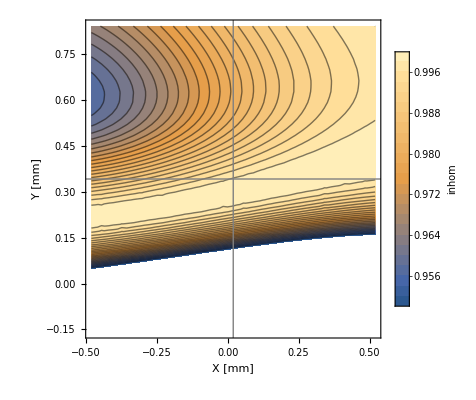

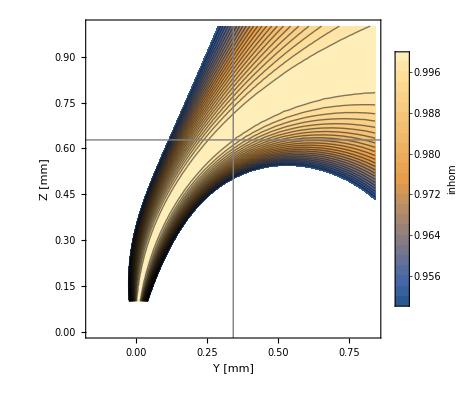

```mathematica
ContourPlot[XCosineAccurateC2[x/1000,y/1000,z1],{x,x1/mm-.5,x1/mm+.5},{y,y1/mm-.5,y1/mm+.5},Contours->Table[i,{i,1,.95,-.002}],PlotPoints->15,PlotRange->{.95,1},PlotLegends->BarLegend[All,LegendLabel->"inhom",LabelStyle->{Bold,Gray,16}],
Epilog->{Gray,Thick,Line[{{-1,1000y1},{1,1000y1}}],Gray,Thick,Line[{{1000x1,-1},{1000x1,1.0}}]},
LabelStyle->{Gray,Bold,16},FrameLabel->{"X [mm]","Y [mm]"}]

ContourPlot[XCosineAccurateC2[x1,y mm,z mm],{y,y1/mm-.5,y1/mm+.5},{z,0.1,1},Contours->Table[i,{i,1,.95,-.002}],PlotPoints->15,PlotRange->{.95,1},PlotLegends->BarLegend[All,LegendLabel->"inhom",LabelStyle->{Bold,Gray,16}],
Epilog->{Gray,Thick,Line[{{-1,1000z1},{1,1000z1}}],Gray,Thick,Line[{{1000y1,-1},{1000y1,1.0}}]},
LabelStyle->{Gray,Bold,16},FrameLabel->{"Y [mm]","Z [mm]"}]
```

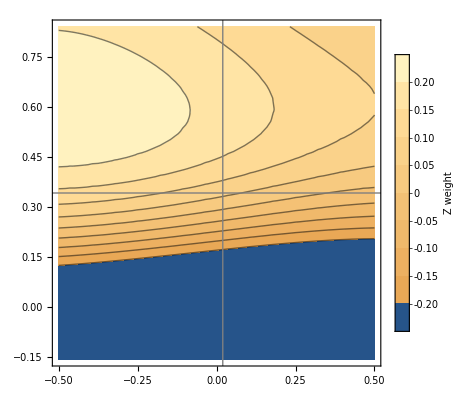

```mathematica
ContourPlot[BChipDirection[x mm,y mm,z1][[3]],{x,-.5,.5},{y,y1/mm-.5,y1/mm+.5},Contours->Table[i,{i,-.2,.2,.05}],PlotLegends->BarLegend[All,LegendLabel->"Z weight",LabelStyle->Directive[Brown,FontSize->14,Italic]],Epilog->{Gray,Thick,Line[{{-1,1000y1},{1,1000y1}}],Gray,Thick,Line[{{1000x1,-1},{1000x1,1.0}}]},LabelStyle->{Gray,Bold,16}]
```

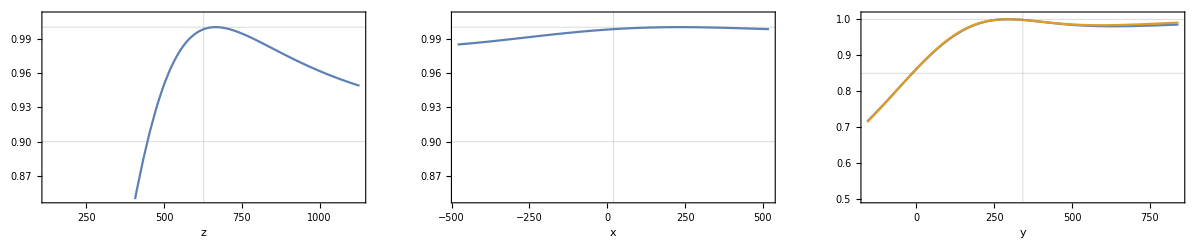

```mathematica
GraphicsGrid[{{
Plot[XCosineAccurateC2[x1,y1,z μm],{z,z1/μm-1000/2,z1/μm+1000/2},AxesOrigin->{z1/μm,0},Axes->False,Frame->True,GridLines->{{z1/μm},{.9,1.0}},PlotRange->{.85,1.01},FrameLabel->{"z"}],
Plot[XCosineAccurateC2[x μm,y1,z1],{x,x1/μm-1000/2,x1/μm+1000/2},Axes->False,Frame->True,GridLines->{{x1/μm},{.9,1.0}},PlotRange->{0.85,1.01},FrameLabel->{"x"}],
Plot[{XCosineAccurateC2[x1,y μm,z1],
XCosine[x1,y μm,z1]},{y,y1/μm-1000/2,y1/μm+1000/2},Axes->False,Frame->True,GridLines->{{y1/μm},{.85,1.0}},PlotRange->{0.5,1.01},FrameLabel->{"y"}]}}]
```

### Definition of adiabatic potentials; rotating-frame + RWA (this is equivalent to Δ Fz + (Ω/2) Fx + Zeeman energies (note Perrin/Garraway papers just use Ω_0 Fx)

```mathematica
Clear[AdiabaticEnergiesChipC,AdiabaticEnergiesChipC2,AdiabaticEnergiesChipC2All]
AdiabaticEnergiesChipSlow[Δ_,Ω_,x_,y_,z_]:=Max[Eigenvalues[ ({{2Δ, Ω/2, 0, 0, 0}, {Ω/2, Δ, Sqrt[3/2]Ω /2, 0, 0}, {0, Sqrt[3/2] Ω /2, 0, Sqrt[3/2]Ω /2, 0}, {0, 0, Sqrt[3/2]Ω /2, -Δ, Ω /2}, {0, 0, 0, Ω /2, -2Δ}})+({{ZeemanShift[BChipMag[x,y,z]][[1]], 0, 0, 0, 0}, {0, ZeemanShift[BChipMag[x,y,z]][[2]], 0, 0, 0}, {0, 0, ZeemanShift[BChipMag[x,y,z]][[3]], 0, 0}, {0, 0, 0, ZeemanShift[BChipMag[x,y,z]][[4]], 0}, {0, 0, 0, 0, ZeemanShift[BChipMag[x,y,z]][[5]]}})]];  
AdiabaticEnergiesChipC[Δ_,Ω_,x_,y_,z_]:=Max[Eigenvalues[ ({{2Δ, Ω/2, 0, 0, 0}, {Ω/2, Δ, Sqrt[3/2]Ω /2, 0, 0}, {0, Sqrt[3/2] Ω /2, 0, Sqrt[3/2]Ω /2, 0}, {0, 0, Sqrt[3/2]Ω /2, -Δ, Ω /2}, {0, 0, 0, Ω /2, -2Δ}})+({{ZeemanShiftC[BChipMagC2[x,y,z]][[1]], 0, 0, 0, 0}, {0, ZeemanShiftC[BChipMagC2[x,y,z]][[2]], 0, 0, 0}, {0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[3]], 0, 0}, {0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[4]], 0}, {0, 0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[5]]}})]];  

AdiabaticEnergiesChipC2[Δ_?NumericQ,Ω_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=AdiabaticEnergiesChipC[Δ, Ω,x,y,z ];

AdiabaticEnergiesChipCAll[Δ_,Ω_,x_,y_,z_]:=Eigenvalues[ ({{2Δ, Ω/2, 0, 0, 0}, {Ω/2, Δ, Sqrt[3/2]Ω /2, 0, 0}, {0, Sqrt[3/2] Ω /2, 0, Sqrt[3/2]Ω /2, 0}, {0, 0, Sqrt[3/2]Ω /2, -Δ, Ω /2}, {0, 0, 0, Ω /2, -2Δ}})+({{ZeemanShiftC[BChipMagC2[x,y,z]][[1]], 0, 0, 0, 0}, {0, ZeemanShiftC[BChipMagC2[x,y,z]][[2]], 0, 0, 0}, {0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[3]], 0, 0}, {0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[4]], 0}, {0, 0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[5]]}})];  (* +MicrowaveShift[x,y,z]   *)    

AdiabaticEnergiesChipC2All[Δ_?NumericQ,Ω_?NumericQ,x_?NumericQ,y_?NumericQ,z_?NumericQ]:=AdiabaticEnergiesChipCAll[Δ, Ω,x,y,z ];

AdiabaticVectorsChipC[Δ_,Ω_,x_,y_,z_]:=Eigenvectors[ ({{2Δ, Ω/2, 0, 0, 0}, {Ω/2, Δ, Sqrt[3/2]Ω /2, 0, 0}, {0, Sqrt[3/2] Ω /2, 0, Sqrt[3/2]Ω /2, 0}, {0, 0, Sqrt[3/2]Ω /2, -Δ, Ω /2}, {0, 0, 0, Ω /2, -2Δ}})+({{ZeemanShiftC[BChipMagC2[x,y,z]][[1]], 0, 0, 0, 0}, {0, ZeemanShiftC[BChipMagC2[x,y,z]][[2]], 0, 0, 0}, {0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[3]], 0, 0}, {0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[4]], 0}, {0, 0, 0, 0, ZeemanShiftC[BChipMagC2[x,y,z]][[5]]}})];
```

```mathematica
1000First@AbsoluteTiming@Table[AdiabaticEnergiesChipSlow[Δ1,Ω1,x1,y1,z1+zi],{zi,.0001,.0002,.00001}]
1000First@AbsoluteTiming@Table[AdiabaticEnergiesChipC[Δ1,Ω1,x1,y1,z1+zi],{zi,.0001,.0002,.00001}]
1000First@AbsoluteTiming@Table[AdiabaticEnergiesChipC2[Δ1,Ω1,x1,y1,z1+zi],{zi,.0001,.0002,.00001}]
```

190.291

63.878

0.0156

## calculate some potentials!

```mathematica
Δguess = (ZeemanShift[B0]//Differences)[[4]]
```

3.47991×10^6

```mathematica
Δ1=Δguess+50*^3;

Ωc =     1.0 16.983*^3;   (* rabi frequency *)  (* taken from German's current of like .02A or something, but with loop coplanar with chip *)
Ωc =    5*^3;
Clear[testf];
testf[x_,y_,z_]:=AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z] MagFracC2[x,y,z ]    ,x,y,z];
t= Table[{z,testf[x1,y1,z]},{z,z1-1.2 mm,z1+1.2mm,0.125*^-6}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
ShiftVal=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]MagFracC2[x1,y1,zmin ],x1,y1,zmin];
testf[x1,y1,z1]nKPerHz;
Ububble[x_,y_,z_]:= testf[x,y,z]-ShiftVal;
Plot[Ububble[x1,y1,z],{z,z1-.0002,z1+.0002},PlotRange->{0,10000}];
```

```mathematica
BoxSize =.3; (* mm *)
```

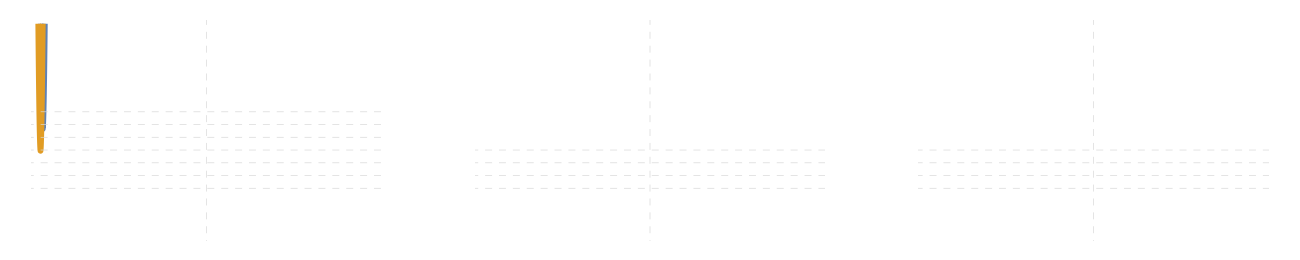

```mathematica
GraphicsGrid[{{Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x1,y1,z/1000-1*^-6]),
(-ShiftVal+ AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x1,y1,z/1000] MagFracC2[x1,y1,z mm],x1,y1,z mm])
},{z,1000z1-BoxSize/4,1000z1+BoxSize/4},PlotRange->{-100,250},PlotStyle->Thickness[.01],PlotPoints->300,FrameStyle->Directive[Black,12,FontFamily->"Century Gothic"],Axes->False,GridLines->{{1000z1},{0,21,-21,42,63,84,105}},GridLinesStyle->Dashed,FrameLabel->{"Z [mm]","Energy [Hz]"}],
Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x1,y/1000-1*^-6,z1]),
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc   XCosineAccurateC2[x1,y/1000,z1]MagFracC2[x1,y mm,z1]  ,x1,y/1000,z1])},
{y,y1/mm-BoxSize/4,y1/mm+BoxSize/4},
PlotRange->{-100,250},PlotStyle->Thickness[.01],
FrameStyle->Directive[Black,12,FontFamily->"Century Gothic"],Axes->False,
GridLines->{{1000y1},{0,21,-21,42}},GridLinesStyle->Dashed,FrameLabel->{"Y (mm)","Energy (Hz)"}],
Plot[{
(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  ,x/1000-1*^-6,y1,z1]),
(-ShiftVal+1+AdiabaticEnergiesChipC2[Δ1, Ωc XCosineAccurateC2[x/1000,y1,z1]MagFracC2[x/1000,y1,z1] ,x/1000,y1,z1])},
{x,x1/mm-BoxSize/2, x1/mm+BoxSize/2},PlotRange->{-100,250},PlotPoints->200,PlotStyle->Thickness[.01],FrameStyle->Directive[Black,12,FontFamily->"Century Gothic"],Axes->False,GridLinesStyle->Dashed,GridLines->{{1000x1},{0,21,-21,42}},FrameLabel->{"X (mm)","Energy (Hz)"}]}},ImageSize->1300]
```

```mathematica
ftight =150;
fweak = 50;
AtomNumber =200000;
fbar = (ftight  ftight fweak)^.33333;
abar= Sqrt[hbar/(mRb 2 π fbar)];
μ= (hbar 2 π fbar/2)(15 AtomNumber (100.4 .529177*^-10)/abar)^(2/5);
Print[μnK = μ /kb/1*^-9 //Round , " nK"] 
Print[μHz =μnK 21 //Round, " Hz"] 
Print["Tight TF radius = ", Round[1*^6 Sqrt[2μ/(mRb 4 π^2 ftight^2)]], " μm"]
Print["Loose TF radius = ", Round[1*^6 Sqrt[2μ/(mRb 4 π^2 fweak^2)]], " μm"]
```

117 nK

2457 Hz

Tight TF radius = 5 μm

Loose TF radius = 15 μm

```mathematica
graining = .1*^-6;
t= Table[{z,testf[x1,y1,z]},{z,z1-.5 mm,z1+.001mm,graining}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
minval = t[[minloc,2]] h/kb/1*^-9;
Print[minval, " nK at location z = ",1000 zmin, " mm"]
Print["fz = ",fz = Sqrt[h(t[[minloc+1,2]]-2t[[minloc,2]]+t[[minloc-1,2]])/graining^2/mRb]/2/π, " Hz"]
Print["SHO minimum ", SHOnKz=h fz/kb/1*^-9/2, " nK, ", fz/2, " Hz"]
minval+SHOnKz //Round
```

529.317 nK at location z = 0.554037 mm

fz = 211.722 Hz

SHO minimum 5.08052 nK, 105.861 Hz

534

```mathematica
graining = .1*^-6;
t= Table[{z,testf[x1,y1,z]},{z,z1-.001 mm,z1+3.0mm,graining}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[Position[t[[All,2]],Min[t[[All,2]]]][[1,1]],1]];
minval = t[[minloc,2]] h/kb/1*^-9;
Print[minval, " nK at location z = ",1000 zmin, " mm"]
Print["fz = ",fz = Sqrt[h(t[[minloc+1,2]]-2t[[minloc,2]]+t[[minloc-1,2]])/graining^2/mRb]/2/π, " Hz"]
Print["SHO minimum ", SHOnKz=h fz/kb/1*^-9/2, " nK, ", fz/2, " Hz"]
minval+SHOnKz //Round
```

527.352 nK at location z = 0.719337 mm

fz = 137.236 Hz

SHO minimum 3.29315 nK, 68.6181 Hz

531

```mathematica
ty= Table[{y,testf[x1,y,z1]},{y,y1-.001,y1+0.001,graining}];
minlocy= Position[ty[[All,2]],Min[ty[[All,2]]]][[1,1]];
ymin = ty[[Position[ty[[All,2]],Min[ty[[All,2]]]][[1,1]],1]];
minvaly = ty[[minlocy,2]] h /kb/1*^-9;
Print[minvaly, " nK at location y = ",1000 ymin, " mm"]
Print["fy = ",fy=Sqrt[h(ty[[minlocy+1,2]]-2ty[[minlocy,2]]+ty[[minlocy-1,2]])/graining^2/mRb]/2/π]
Print["SHO minimum ", SHOnKy=h fy/kb/1*^-9/2, " nK, ", fy/2, " Hz"]
minvaly+SHOnKy //Round
```

$Aborted

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of {} does not exist.

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

0.0479924 ty⟦{{}}⟦1,1⟧,2⟧ nK at location y = 1000 ty⟦{{}}⟦1,1⟧,1⟧ mm

Part::pkspec1: The expression 1+{{}}⟦1,1⟧ cannot be used as a part specification.

Part::pkspec1: The expression {{}}⟦1,1⟧ cannot be used as a part specification.

Part::pkspec1: The expression -1+{{}}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

fy = 107.843 √(ty⟦-1+{{}}⟦1,1⟧,2⟧-2 ty⟦{{}}⟦1,1⟧,2⟧+ty⟦1+{{}}⟦1,1⟧,2⟧)

SHO minimum 2.58782 √(ty⟦-1+{{}}⟦1,1⟧,2⟧-2 ty⟦{{}}⟦1,1⟧,2⟧+ty⟦1+{{}}⟦1,1⟧,2⟧) nK, 53.9214 √(ty⟦-1+{{}}⟦1,1⟧,2⟧-2 ty⟦{{}}⟦1,1⟧,2⟧+ty⟦1+{{}}⟦1,1⟧,2⟧) Hz

Round[0.0479924 ty⟦{{}}⟦1,1⟧,2⟧+2.58782 √(ty⟦-1+{{}}⟦1,1⟧,2⟧-2 ty⟦{{}}⟦1,1⟧,2⟧+ty⟦1+{{}}⟦1,1⟧,2⟧)]

```mathematica
tx= Table[{x,testf[x,y1,z1]},{x,x1-.001,x1+0.001,graining}];
minlocx= Position[tx[[All,2]],Min[tx[[All,2]]]][[1,1]];
xmin = tx[[Position[tx[[All,2]],Min[tx[[All,2]]]][[1,1]],1]];
minvalx = tx[[minlocx,2]]h /kb/1*^-9;
Print[minvalx, " nK at location yx= ",1000 xmin, " mm"]
Print["fx = ",fx=Sqrt[h(tx[[minlocx+1,2]]-2tx[[minlocx,2]]+tx[[minlocx-1,2]])/graining^2/mRb]/2/π]
Print["SHO minimum ", SHOnKx=h fx/kb/1*^-9/2, " nK, ", fx/2, " Hz"]
minvalx+ SHOnKx //Round
```

529.723 nK at location yx= -0.173095 mm

fx = 73.3204

SHO minimum 1.75941 nK, 36.6602 Hz

531

```mathematica
λ = 10064*^-9;
```

```mathematica
a1= ContourPlot[0 3000 Sin[2 π x mm/λ]^2 1*^9(h/kb)+(-ShiftVal+AdiabaticEnergiesChipC2[Δ1,Ωc XCosineAccurateC2[x/1000,y/1000,z1] MagFracC2[x/1000,y/1000,z1]  ,x/1000,y/1000,z1]),
{x,1000x1-BoxSize/2,1000x1+BoxSize/2},{y,1000y1-BoxSize/4,1000y1+BoxSize/4},
PlotRange->{-500,1000},
AspectRatio->1/2,
Contours->Table[i,{i,-500,1000,100}],
PlotPoints->102,ImageSize->1000,
FrameLabel->{"X (mm)","Y (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,
Epilog->{Red,Thin,Line[{{1000x1-.2,1000y1},{1000x1+.2,1000y1}}],Red,Thin,Line[{{1000x1,1000y1-.21},{1000x1,1000y1+.2}}]}]  (*takes ~10s to generate *)
```

$Aborted

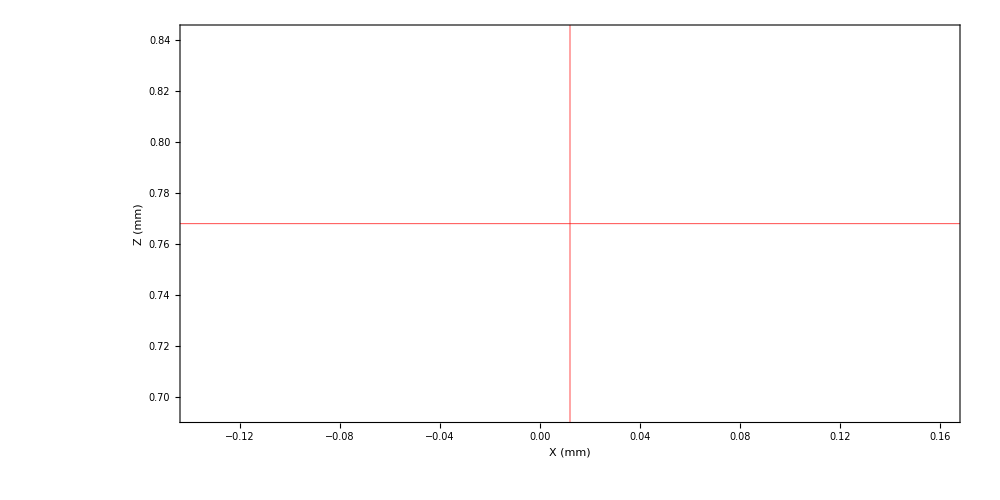

```mathematica
ContourPlot[nKPerHz(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x/1000,y1,z/1000] MagFracC2[x/1000,y1,z/1000],x/1000,y1,z/1000]),{x,1000x1-BoxSize/2,1000x1+BoxSize/2},
{z,1000z1-BoxSize/4,1000z1+BoxSize/4},
PlotRange->{-100,200},ImageSize->1000,
Contours->Table[i,{i,-100,200,10}],PlotPoints->140,
FrameLabel->{"X (mm)","Z (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,AspectRatio->1/2,
Epilog->{Red,Thickness[.0005],Line[{{-.2,1000z1},{.2,1000z1}}],Red,Thickness[.0005],Line[{{1000x1,.2},{1000x1,1.0}}]}]  (*takes ~10s to generate *)   (* GridLines->{Table[i,{i,x1/mm-.08,x1/mm+.08,.0045}],Table[i,{i,z1/mm-.04,z1/mm+.04,.0045}]} *)
```

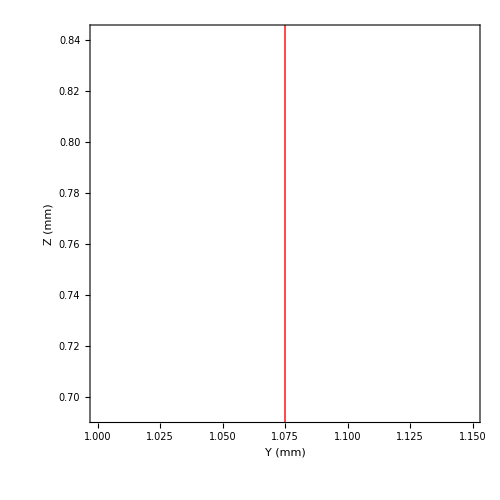

```mathematica
a1= ContourPlot[nKPerHz(-ShiftVal+AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x1,y/1000,z/1000] MagFracC2[x1,y/1000,z/1000],x1,y/1000,z/1000]),{y,1000y1-BoxSize/4,1000y1+BoxSize/4},
{z,1000z1-BoxSize/4,1000z1+BoxSize/4},PlotRange->{-100,200},
Contours->Table[i,{i,-100,200,20}],PlotPoints->40,
AspectRatio->1,
ImageSize->500,
FrameLabel->{"Y (mm)","Z (mm)"},
FrameStyle->Directive[Thick,Black,12,FontFamily->"Century Gothic"],
Axes->False,Epilog->{Red,Thin,Line[{{-.2,1000z1},{.1,1000z1}}],Red,Thin,Line[{{1000y1,.4},{1000y1,1.0}}]}]  (*takes ~10s to generate *)
```

```mathematica
Print["z1 = ", Round[1*^6 z1], " microns"]
```

z1 = 768 microns

```mathematica
Δ1= 1.969*^6;
Δ1 =1.97*^6; 
Δ1 = 3.8935*^6;
Δ1 = 3.897*^6;
Δ1 =3.909036*^6;
Δ1= 1.786*^6;
Δ1=2.647*^6;
Δ1=1.350*^6;
Δ1= 1.375*^6;
Δ1=2.540*^6+40*^3;
Δ1=2.500*^6+0*^3;

Δ1=3.728*^6;

Δ1=1.970*^6;
Δ1=1.970*^6+40*^3;

Δ1=Δguess+30*^3;



Ωc = .25   16.983*^3;   (* rabi frequency *)  (* taken from German's current of like .02A or something, but with loop coplanar with chip *)
Ωc =5*^3;(* rabi frequency *)
```

## Test

```mathematica
TestBECPotential[x_,y_,z_,ω_]:= (1/2) (mRb/h) ω^2 (x^2+y^2+z^2)
```

```mathematica
fTest= 100;
```

```mathematica
potential0 = Table[TestBECPotential[x,y,z,2Pi fTest],
{z,-CubeSize/4,+CubeSize/4,DataFileGraining},
{y,-CubeSize/4,+CubeSize/4,DataFileGraining},
{x,-CubeSize/2,+CubeSize/2,DataFileGraining}];
```

Table::iterb: Iterator {z,-CubeSize/4,CubeSize/4,DataFileGraining} does not have appropriate bounds.

```mathematica
Dimensions[potential0]
```

{4}

```mathematica
potential0[0,0,z1-CubeSize/4,628]
```

Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}][0,0,0.000767871-CubeSize/4,628]

```mathematica
ListPlot[potential0[[51,;;,101]]]
```

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}] does not exist.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2. 3.141592653589793 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}] does not exist.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

Part::partw: Part 51 of Table[TestBECPotential[x,y,z,2. 3.14159 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Table::iterb: Iterator {z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining} does not have appropriate bounds.

General::stop: Further output of Table::iterb will be suppressed during this calculation.

ListPlot::lpn: Table[TestBECPotential[x,y,z,2. 3.14159 fTest],{z,-0.25 CubeSize,0.25 CubeSize,DataFileGraining},{y,(-1. CubeSize) 0.25,+CubeSize 0.25,DataFileGraining},{x,(-1. CubeSize) 0.5,+CubeSize 0.5,DataFileGraining}]⟦51,1;;All,101⟧ is not a list of numbers or pairs of numbers.

ListPlot[Table[TestBECPotential[x,y,z,2 π fTest],{z,-CubeSize/4,CubeSize/4,DataFileGraining},{y,-CubeSize/4,(+CubeSize)/4,DataFileGraining},{x,-CubeSize/2,(+CubeSize)/2,DataFileGraining}]⟦51,1;;All,101⟧]

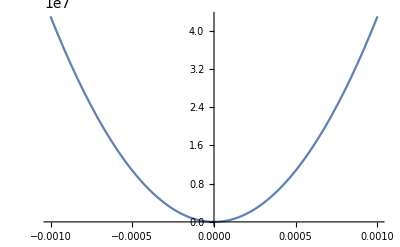

```mathematica
Plot[TestBECPotential[0,0,x,2 Pi 100],{x,-.001,.001}]
```

```mathematica
potential0a=Flatten[potential0,1];
Dimensions[potential0a]
FileString0=StringJoin["TestPotential_",ToString[1000DataFileGraining/μm//Round],"u_",ToString[fTest //Round],"Hz",".csv"]
"TestPotential_250u_100Hz.csv"
```

Table::iterb: Iterator {z,-CubeSize/4,CubeSize/4,DataFileGraining} does not have appropriate bounds.

{4}

TestPotential_Round[1000000000 DataFileGraining]u_100Hz.csv

TestPotential_250u_100Hz.csv

```mathematica
Export[FileString0,potential0a]
```

TestPotential_Round[1000000000 DataFileGraining]u_100Hz.csv

```mathematica
CenterPoint=Length[potential0]/2//Ceiling
```

2

## Real ones

```mathematica
PotentialType ="Trap2_";
PotentialType ="Trap1_";
PotentialType ="Trap4_";
```

```mathematica
t= Table[{z,testf[x1,y1,z]},{z,.2 mm,z1+20 μm,1*^-6}];
minloc= Position[t[[All,2]],Min[t[[All,2]]]][[1,1]];
zmin = t[[minloc,1]];
ShiftVal=AdiabaticEnergiesChipC2[Δ1,Ωc  XCosineAccurateC2[x1,y1,zmin]MagFracC2[x1,y1,zmin ],x1,y1,zmin]

CubeSize= 100μm;
CubeSize= 50μm;
CubeSize= 350μm;
CubeSize= 150μm;
CubeSize= 400μm;
CubeSize= 300μm;

DataFileGraining = 0.5μm;
DataFileGraining = 0.8μm;
DataFileGraining = 1.0μm;
```

8009.5

```mathematica
Beep[];
```

```mathematica
Parallelize[potential1=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];] //AbsoluteTiming
```

$Aborted

```mathematica
Dimensions[potential1]
```

{151,151,301}

```mathematica
potential1a=Flatten[potential1,1];
Dimensions[potential1a]
```

{22801,301}

```mathematica
FileString1=StringJoin["CALpotential_",PotentialType,ToString[1000 DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3 //Round],"_o",ToString[Ωc//Round],"_hom.csv"]
```

CALpotential_Trap4_1000nm_d3029_o5000_hom.csv

```mathematica
Parallelize[potential2=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z]    ,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];]
Dimensions[potential2]
potential2a=Flatten[potential2,1];
Dimensions[potential2a]
```

$Aborted

{}

Flatten::normal: Nonatomic expression expected at position 1 in Flatten[potential2,1].

{2}

```mathematica
FileString2=StringJoin["CALpotential_",PotentialType,ToString[1000 DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3//Round],"_o",ToString[Ωc//Round],"_inhom1.csv"]
```

CALpotential_Trap4_1000nm_d3029_o5000_inhom1.csv

```mathematica
Parallelize[potential3=-ShiftVal+Table[AdiabaticEnergiesChipC2[Δ1, Ωc  XCosineAccurateC2[x,y,z] MagFracC2[x,y,z ]   ,x,y,z],
{z,z1-CubeSize/4,z1+CubeSize/4,DataFileGraining},
{y,y1-CubeSize/4,y1+CubeSize/4,DataFileGraining},
{x,x1-CubeSize/2,x1+CubeSize/2,DataFileGraining}];]
Dimensions[potential3]
potential3a=Flatten[potential3,1];
Dimensions[potential3a]
```

{151,151,301}

{22801,301}

```mathematica
FileString3=StringJoin["CALpotential_",PotentialType,ToString[1000DataFileGraining/μm//Round],"nm_d",ToString[Δ1/1*^3 //Round],"_o",ToString[Ωc//Round],"_inhom2.csv"]
```

CALpotential_Trap4_1000nm_d3029_o5000_inhom2.csv

```mathematica
4+4
```

8

```mathematica
Directory[]
```

C:\Users\josep\Documents

```mathematica
SetDirectory["/Users/nlundbla/Documents"];
```

SetDirectory::cdir: Cannot set current directory to /Users/nlundbla/Documents.

```mathematica
(* SetDirectory["/Volumes/GoogleDrive/My Drive/Mathematica Files/NASA CAL/potentials"] *)
```

```mathematica
Export[FileString3,potential3a]
```

CALpotential_Trap4_1000nm_d3029_o5000_inhom2.csv

```mathematica
CopyFile["CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv","/Volumes/GoogleDrive/My Drive/Mathematica Files/NASA CAL/potentials/CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv"];
```

```mathematica
DeleteFile["CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv"];
```

DeleteFile::fdnfnd: Directory or file CALpotential_Trap2_1000nm_d2010_o5000_inhom2.csv not found.

```mathematica
Export[FileString1,potential1a]
Export[FileString2,potential2a]
```

CALpotential_Trap4_1000nm_d3029_o5000_hom.csv

CALpotential_Trap4_1000nm_d3029_o5000_inhom1.csv

```mathematica
CenterPoint=Length[potential3]/2//Ceiling
```

76

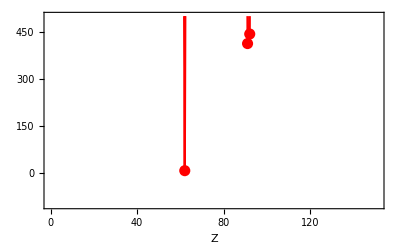

```mathematica
ListPlot[(potential3[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-100,500},PlotStyle->{Red,PointSize[.02]},Joined->True,Mesh->All,  Frame->True,Axes->False,FrameLabel->{"Z"}]
```

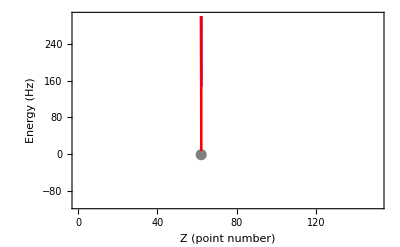

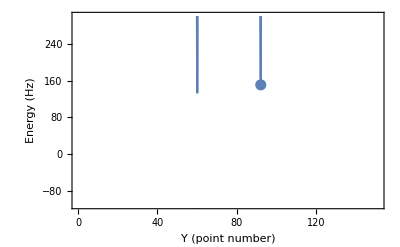

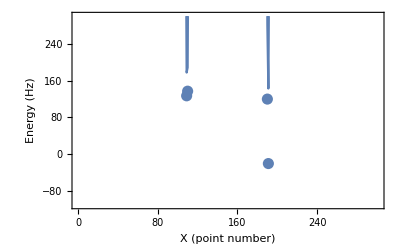

```mathematica
Show[
ListPlot[(potential1[[;;,CenterPoint,2 CenterPoint]]),PlotRange->{-110,300},PlotStyle->{PointSize[.02],Blue},Joined->True,Frame->True,Axes->False,FrameLabel->{"Z (point number)","Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential2[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->{PointSize[.02],Gray},Joined->False,Frame->True,Axes->False,FrameLabel->{"Z (point number)","Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential3[[;;,CenterPoint,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->{Red,PointSize[.02]},Joined->True,Frame->True,Axes->False,FrameLabel->{"Z"}]]
Show[ListPlot[(potential1[[CenterPoint,;;,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->True,Frame->True,Axes->False,FrameLabel->{"Y (point number)", "Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]},FrameStyle->Directive[14,FontFamily->"Century Gothic"]],
ListPlot[(potential2[[CenterPoint,;;,2CenterPoint]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->False,Frame->True,Axes->False]]
Show[ListPlot[(potential1[[CenterPoint,CenterPoint,;;]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->True,Frame->True,Axes->False,FrameStyle->Directive[14,FontFamily->"Century Gothic"],FrameLabel->{"X (point number)", "Energy (Hz)",StringJoin[ToString[DataFileGraining/μm]," μm graining"]}],
ListPlot[(potential2[[CenterPoint,CenterPoint,;;]]),PlotRange->{-110,300},PlotStyle->PointSize[.02],Joined->False,Frame->True,Axes->False,FrameLabel->{"X"}]]
```

```mathematica
Manipulate[ListContourPlot[nKPerHz potential1[[i]],PlotRange->{-10,50},Contours->10],{i,1,Length[potential1],1}]
```

Part::partd: Part specification potential1⟦1⟧ is longer than depth of object.

ListContourPlot::arrayerr: 0.0479924 potential1⟦1⟧ must be a valid array.

Part::partd: Part specification potential1⟦1⟧ is longer than depth of object.

ListContourPlot::arrayerr: 0.0479924 potential1⟦1⟧ must be a valid array.

Part::partd: Part specification potential1⟦1⟧ is longer than depth of object.

ListContourPlot::arrayerr: 0.0479924 potential1⟦1⟧ must be a valid array.

### Look at all levels; motivated by some E. Elliott concerns?

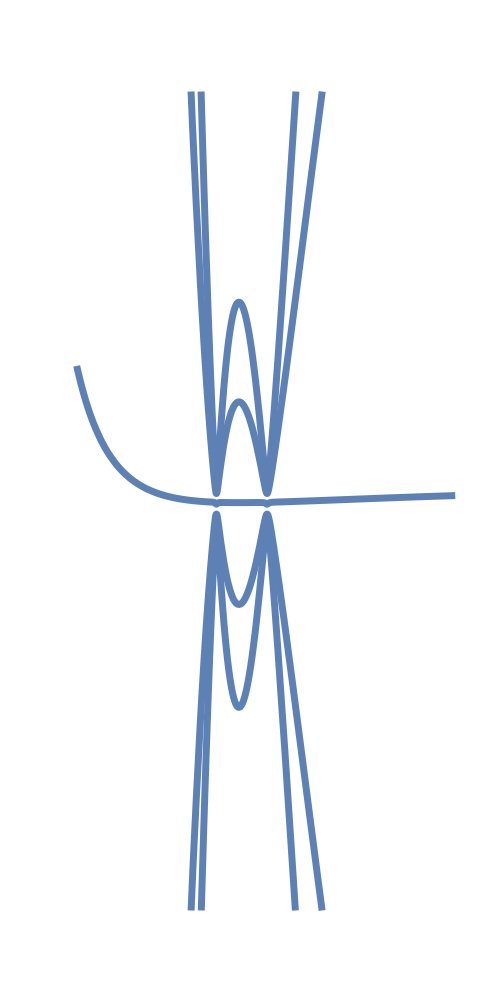

```mathematica
c=Plot[(-ShiftVal+Sort[AdiabaticEnergiesChipC2All[Δguess+250000,    10Ωc   ,x1,y1,z/1000]])/1*^6,
{z,1000z1-.3,1000z1+.4},
PlotRange->{-1,1},
PlotStyle->Thickness[.01],
AspectRatio->2,
Axes->False,
FrameStyle->Directive[Thickness[.01],White,28,FontFamily->"Century Gothic"],
FrameLabel->{"Z [mm]","Energy [MHz]"}]
```

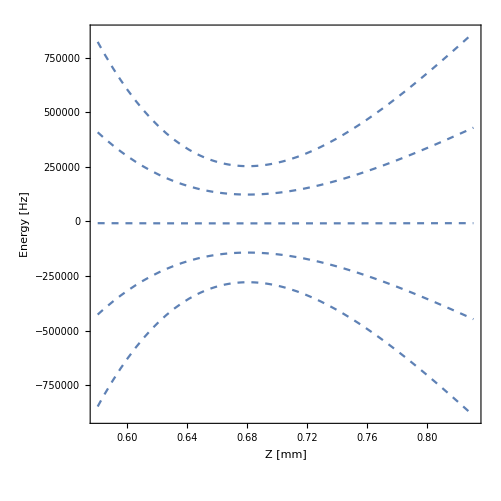

-Graphics-